# Support Vector Machines

In this notebook we will develop support vector machine models for several datasets by using them to formulate a constrained optimisation problem. First, we review how constrained optimisation is done in Mathematica.

## Constrained Optimisation

Consider the problem of minimising x^2+y^2 subject to the constraints 3x+2y≥7 and x+2y≥6. We can solve this using NMinimize:

```mathematica
NMinimize[{x^2+y^2,And[3x+2y≥7,x+2y≥6]},{x,y}]
```

{7.2,{x→1.2,y→2.4}}

Let’s visualise the solution along with the constraints and the function we are trying to minimise.

```mathematica
Show[Plot3D[{x^2+y^2},{x,0,5},{y,0,5},RegionFunction->Function[{x,y},3x+2y≥7&&x+2y≥6]],ListPointPlot3D[{{1.2,2.4,7.2}}],Graphics3D[{Opacity[0.5],Gray,InfinitePlane[Table[{x,1/2 (7-3 x),RandomReal[]},{x,3}]]}],Graphics3D[{Opacity[0.5],Gray,InfinitePlane[Table[{x,1/2 (6- x),RandomReal[]},{x,3}]]}]]
```

-Graphics3D-

## Linear Support Vector Machine

Let’s now produce a support vector machine for the example from the video lectures. First, we need to define the samples, x_i. These are points in a 2D vector space which are labelled as either “Plus” or “Minus”.

```mathematica
data=<|"Plus"->{{1.284422952732416,2.481901856407326},{1.4879960382523703,2.402086883623099},{4.193340935618989,2.0674820899685353},{1.07511361074236,2.8655605261563037},{4.5621522276001985,2.3036590135818598},{0.0734941576442104,2.7567100412409644},{2.0267587486366514,1.8146817202743937},{1.7160467347301873,2.2314527869285374}},"Minus"->{{0.3650725217541822,1.4540111456859945},{1.8799169703454597,1.3235540770631689},{0.2775167301897557,0.026781782266628973},{1.7185797382262036,0.8439744313421516},{1.0440125841941863,0.8714161830961258},{4.009012707820185,0.4883132746354524},{0.0444111436444237,1.0249991478151106},{1.4175016236764821,0.3949618274790252},{0.40287782851680287,0.35796696425588426},{1.3129335119181957,0.193320544474747},{1.6678854129083547,0.5245058562945744},{3.62477502445507,0.2321920742831569}}|>;
```

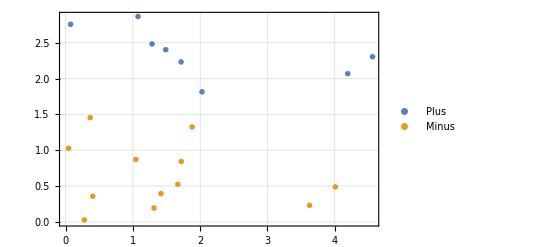

```mathematica
ListPlot[data,PlotMarkers->"OpenMarkers",PlotTheme->"Detailed"]
```

### Solving the primal problem

We can directly solve the primal problem. To do so we need to set up the constraints imposed by the samples.

```mathematica
plusConstraints=Apply[And,Table[{w1,w2}.x+b≥1,{x,data["Plus"]}]]
```

b+1.28442 w1+2.4819 w2≥1&&b+1.488 w1+2.40209 w2≥1&&b+4.19334 w1+2.06748 w2≥1&&b+1.07511 w1+2.86556 w2≥1&&b+4.56215 w1+2.30366 w2≥1&&b+0.0734942 w1+2.75671 w2≥1&&b+2.02676 w1+1.81468 w2≥1&&b+1.71605 w1+2.23145 w2≥1

```mathematica
minusConstraints=Apply[And,Table[{w1,w2}.x+b≤-1,{x,data["Minus"]}]]
```

b+0.365073 w1+1.45401 w2≤-1&&b+1.87992 w1+1.32355 w2≤-1&&b+0.277517 w1+0.0267818 w2≤-1&&b+1.71858 w1+0.843974 w2≤-1&&b+1.04401 w1+0.871416 w2≤-1&&b+4.00901 w1+0.488313 w2≤-1&&b+0.0444111 w1+1.025 w2≤-1&&b+1.4175 w1+0.394962 w2≤-1&&b+0.402878 w1+0.357967 w2≤-1&&b+1.31293 w1+0.193321 w2≤-1&&b+1.66789 w1+0.524506 w2≤-1&&b+3.62478 w1+0.232192 w2≤-1

```mathematica
allConstraints=Join[plusConstraints,minusConstraints];
```

Now we can use NMinimise to find the  solution to the constrained optimisation problem.

```mathematica
{norm2,sol}=NMinimize[{1/2(w1^2+w2^2),allConstraints},{w1,w2,b}]
```

{7.61125,{w1→1.11765,w2→3.7381,b→-8.04866}}

This means that our decision function is

```mathematica
decision[x_]:={1.1176497303899737,3.738096096794236}.x+(-8.048661024444451)
```

Then, our decision line is

```mathematica
Solve[decision[{x,y}]==0,y]
```

{{y→0.267516 (8.04866-1.11765 x)}}

and our margins are

```mathematica
Solve[decision[{x,y}]==1,y]
```

{{y→0.267516 (9.04866-1.11765 x)}}

```mathematica
Solve[decision[{x,y}]==-1,y]
```

{{y→0.267516 (7.04866-1.11765 x)}}

Let’s now plot our decision line, margins and data points

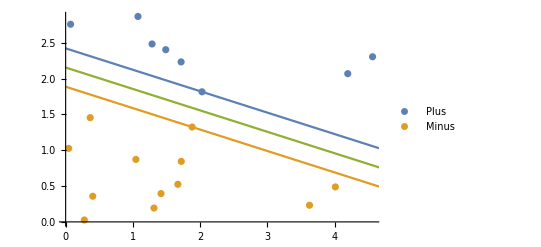

```mathematica
Show[ListPlot[data],Plot[{0.2675158621142974 (9.048661024444451-1.1176497303899737 x),0.2675158621142974 (7.048661024444451-1.1176497303899737 x),0.2675158621142974 (8.048661024444451-1.1176497303899737 x)},{x,0,5}]]
```

### Solving the dual problem

We could also solve the dual problem. First, we build up the matrix X and vectors y, λ and e.

```mathematica
X=Join[data["Plus"],-data["Minus"]];
```

```mathematica
Y=Join[ConstantArray[1,Length[data["Plus"]]],ConstantArray[-1,Length[data["Minus"]]]];
```

```mathematica
e=ConstantArray[1,Length[X]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
λ=Table[λi[i],{i,Length[X]}]
```

{λi[1],λi[2],λi[3],λi[4],λi[5],λi[6],λi[7],λi[8],λi[9],λi[10],λi[11],λi[12],λi[13],λi[14],λi[15],λi[16],λi[17],λi[18],λi[19],λi[20]}

Now we can solve the dual optimisation problem

```mathematica
{max,solλ}=NMaximize[{-1/2 λ.X.Transpose[X].λ+λ.e,λ>0,λ.Y==0},λ]
```

{7.61125,{λi[1]→5.88045×10^-7,λi[2]→4.00756×10^-9,λi[3]→0.,λi[4]→0.,λi[5]→0.,λi[6]→4.50942×10^-8,λi[7]→7.61184,λi[8]→6.56399×10^-8,λi[9]→0.,λi[10]→7.61184,λi[11]→0.,λi[12]→0.,λi[13]→0.,λi[14]→0.,λi[15]→0.,λi[16]→0.,λi[17]→0.,λi[18]→0.,λi[19]→0.,λi[20]→0.}}

Notice that only a small number of the λ_i’s are non-zero; these are the ones corresponding to the support vectors.

We can next compute the value for w=X^T λ and find b from one of the constraints with a non-zero λ_i actually being an equality (rather than an inequality).

```mathematica
wsolλ=Thread[{w1,w2}->Transpose[X].λ/.solλ]
```

{w1→1.11774,w2→3.73838}

```mathematica
bsolλ=Solve[plusConstraints[[7]]/.wsolλ/.GreaterEqual->Equal,b][[1]]
```

{b→-8.04936}

Check this agrees with what we found when solving the primal version

```mathematica
sol
```

{w1→1.11765,w2→3.7381,b→-8.04866}

Knowing the support vectors, we could also go the other way and obtain the λ’s from the w and b found by solving the primal problem

```mathematica
Inverse[Transpose[X[[{7,10}]]]].({w1,w2}/.sol)
```

{7.61125,7.61125}

Again, this is consistent with solving the dual problem.

## Kernel Trick

We next look at an example where the data is not linearly separable and we will have to apply the kernel trick. First we generate two datasets, one surrounding another. We do this by defining the data in polar coordinates:

```mathematica
SeedRandom[1];
```

```mathematica
r1=RandomVariate[UniformDistribution[{0,1}],10];
θ1=RandomReal[{-π,π},10];
```

```mathematica
r2=RandomVariate[NormalDistribution[2,1/10],10];
θ2=RandomReal[{-π,π},10];
```

And then transforming to Cartesian coordinates:

```mathematica
{x1,y1}={r1 Cos[θ1],r1 Sin[θ1]};
{x2,y2}={r2 Cos[θ2],r2 Sin[θ2]};
```

```mathematica
nonsepdata=<|"Plus"->Transpose[{x1,y1}],"Minus"->Transpose[{x2,y2}]|>;
```

We now have a non-linearly separable dataset:

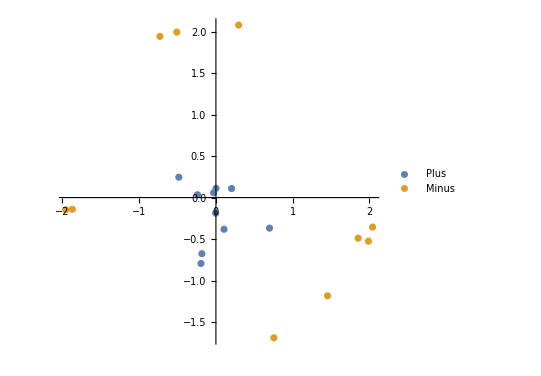

```mathematica
ListPlot[Values[nonsepdata],AspectRatio->Full,PlotLegends->Keys[nonsepdata]]
```

### Explicit polar coordinate map

We first look at the case where we have a good idea for an explicit map ϕ(x,y)=(r,θ) that will transform the data into a nice form. Define the map and apply it to our data:

```mathematica
ϕpolar[{x_,y_}]:={√(x^2+y^2),ArcTan[x,y]};
```

```mathematica
sepdata=Map[ϕpolar,nonsepdata,{2}]
```

<|Plus→{{0.817389,-1.81065},{0.11142,1.56236},{0.789526,-0.484744},{0.187803,-1.58654},{0.241361,2.99816},{0.0657388,2.04306},{0.542247,2.67208},{0.231155,0.490441},{0.396006,-1.30144},{0.700474,-1.83437}},Minus→{{2.07196,-0.172378},{2.0755,1.92995},{1.96364,-3.06723},{1.85056,-1.1506},{2.05836,1.82089},{1.87592,-3.06633},{1.87514,-0.683131},{1.91713,-0.258225},{2.05581,-0.258585},{2.10005,1.42953}}|>

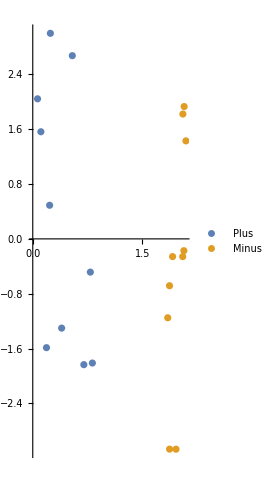

```mathematica
ListPlot[Values[sepdata],AspectRatio->Full,PlotLegends->Keys[sepdata]]
```

Now we build up our X matrix with the transformed samples

```mathematica
X=Join[sepdata["Plus"],-sepdata["Minus"]];
```

```mathematica
Y=Join[ConstantArray[1,Length[sepdata["Plus"]]],ConstantArray[-1,Length[sepdata["Minus"]]]];
```

```mathematica
e=ConstantArray[1,Length[X]];
```

```mathematica
λ=Table[λi[i],{i,Length[X]}];
```

Now we can solve the dual optimisation problem

```mathematica
{max,solλ}=NMaximize[{-1/2 λ.X.Transpose[X].λ+λ.e,λ>0,λ.Y==0},λ];
```

```mathematica
solλ//Chop
```

{λi[1]→1.84272,λi[2]→0,λi[3]→0,λi[4]→0,λi[5]→0,λi[6]→0,λi[7]→0,λi[8]→0,λi[9]→0,λi[10]→0,λi[11]→0,λi[12]→0,λi[13]→0,λi[14]→1.22096,λi[15]→0,λi[16]→0.62176,λi[17]→0,λi[18]→0,λi[19]→0,λi[20]→0}

```mathematica
supportVectors=Pick[Join[nonsepdata["Plus"],nonsepdata["Minus"]],Positive[Chop[λ/.solλ,10^-3]]]
```

{{-0.19418,-0.79399},{0.754913,-1.68958},{-1.87061,-0.141048}}

We can then compute the values for w=X^T λ, and find b from one of the constraints with a non-zero λ_i actually being an equality (rather than inequality).

```mathematica
wsolλ=Thread[{w1,w2}->Transpose[X].λ/.solλ]
```

{w1→-1.91961,w2→-0.0251646}

```mathematica
bsolλ=Solve[{w1,w2}.X[[1]]+b==1/.wsolλ,b][[1]]
```

{b→2.5235}

Now we draw our decision line and margins on the r-θ plot

```mathematica
decisionθ=θ/.Solve[{w1,w2}.{r,θ}+b==fx/.Join[wsolλ,bsolλ],θ][[1]]
```

-39.7383 (-2.5235+1. fx+1.91961 r)

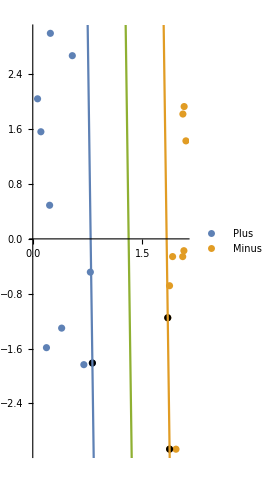

```mathematica
Show[ListPlot[Values[sepdata],AspectRatio->Full,PlotLegends->Keys[sepdata]],ListPlot[Map[ϕpolar,supportVectors],PlotStyle->Black],Plot[Evaluate[decisionθ/.fx->{1,-1,0}],{r,0,2.5}]]
```

We can also draw them on the original plot

```mathematica
decisionr=r/.Solve[{w1,w2}.{r,θ}+b==fx/.Join[wsolλ,bsolλ],r][[1]]
```

-0.520939 (-2.5235+1. fx+0.0251646 θ)

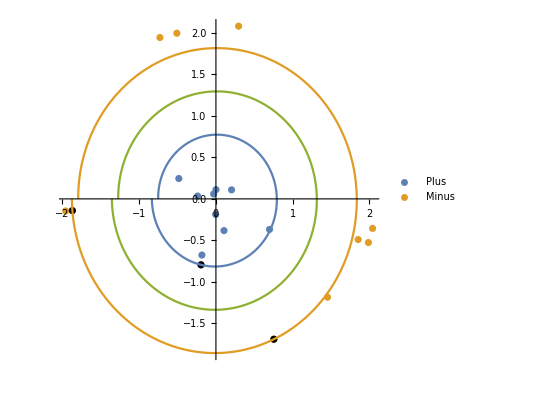

```mathematica
Show[ListPlot[Values[nonsepdata],AspectRatio->Full,PlotLegends->Keys[nonsepdata]],ListPlot[supportVectors,AspectRatio->Full,PlotStyle->Black],PolarPlot[Evaluate[decisionr/.fx->{1,-1,0}],{θ,-π,π}],AspectRatio->Full,PlotRange->All]
```

### Explicit higher map to higher dimensions

There is another way we could get support vector machines to work with this dataset: by projecting onto a higher dimension. We now try the map ϕ(x,y)=(x,y,x^2+y^2)

```mathematica
ϕ3D[{x_,y_}]:={x,y,x^2+y^2};
```

```mathematica
sepdata3D=Map[ϕ3D,nonsepdata,{2}]
```

<|Plus→{{-0.19418,-0.79399,0.668126},{0.000940266,0.111416,0.0124143},{0.698568,-0.367905,0.623351},{-0.00295604,-0.18778,0.03527},{-0.238882,0.0345008,0.0582551},{-0.0299047,0.0585431,0.00432158},{-0.48357,0.245339,0.294031},{0.203907,0.108877,0.0534324},{0.105382,-0.381727,0.156821},{-0.182496,-0.676283,0.490664}},Minus→{{2.04125,-0.355395,4.29301},{-0.729497,1.94307,4.3077},{-1.95821,-0.14589,3.85587},{0.754913,-1.68958,3.42456},{-0.509438,1.99432,4.23684},{-1.87061,-0.141048,3.51906},{1.45436,-1.18364,3.51616},{1.85357,-0.489567,3.67538},{1.98746,-0.525699,4.22637},{0.295681,2.07913,4.41022}}|>

We go through the same process as before to set up the dual optimisation problem:

```mathematica
X=Join[sepdata3D["Plus"],-sepdata3D["Minus"]];
```

```mathematica
Y=Join[ConstantArray[1,Length[sepdata3D["Plus"]]],ConstantArray[-1,Length[sepdata3D["Minus"]]]];
```

```mathematica
e=ConstantArray[1,Length[X]];
```

```mathematica
λ=Table[λi[i],{i,Length[X]}];
```

```mathematica
{max3D,solλ3D}=NMaximize[{-1/2 λ.X.Transpose[X].λ+λ.e,λ>0,λ.Y==0},λ];
```

```mathematica
solλ3D//Chop
```

{λi[1]→0.253444,λi[2]→0,λi[3]→0,λi[4]→0,λi[5]→0,λi[6]→0,λi[7]→0,λi[8]→0,λi[9]→0,λi[10]→0,λi[11]→0,λi[12]→0,λi[13]→0,λi[14]→0.154863,λi[15]→0,λi[16]→0.09858,λi[17]→0,λi[18]→0,λi[19]→0,λi[20]→0}

```mathematica
supportVectors3D=Pick[Join[nonsepdata["Plus"],nonsepdata["Minus"]],Positive[Chop[λ/.solλ,10^-3]]]
```

{{-0.19418,-0.79399},{0.754913,-1.68958},{-1.87061,-0.141048}}

We now compute the values for w=X^T λ and find b from one of the constraints with a non-zero λ_i actually being an equality (rather than inequality).

```mathematica
wsolλ3D=Thread[{w1,w2,w3}->Transpose[X].λ/.solλ3D]
```

{w1→0.0182823,w2→0.0743266,w3→-0.707917}

```mathematica
bsolλ3D=Solve[{w1,w2,w3}.X[[1]]+b==1/.wsolλ3D,b][[1]]
```

{b→1.53554}

Now we draw our decision line and margins on the r-θ plot

```mathematica
decisionz=z0/.Solve[{w1,w2,w3}.{x0,y0,z0}+b==fx/.Join[wsolλ3D,bsolλ3D],z0][[1]]
```

-1.4126 (-1.53554+1. fx-0.0182823 x0-0.0743266 y0)

```mathematica
Show[ListPointPlot3D[Values[sepdata3D]],ListPointPlot3D[ϕ3D/@supportVectors3D,PlotStyle->Black],Plot3D[Evaluate[decisionz/.fx->{1,-1,0}],{x0,-2,2},{y0,-2,2}],PlotRange->All]
```

-Graphics3D-

We can also draw them on the original plot

```mathematica
decisionr=r/.Solve[{w1,w2}.{r,θ}+b==fx/.Join[wsolλ,bsolλ],r][[1]]
```

-0.520939 (-2.5235+1. fx+0.0251646 θ)

```mathematica
Show[ListPlot[Values[nonsepdata],AspectRatio->Full,PlotLegends->Keys[nonsepdata]],ListPlot[supportVectors3D,AspectRatio->Full,PlotStyle->Black],PolarPlot[Evaluate[decisionr/.fx->{1,-1,0}],{θ,-π,π}],AspectRatio->Full,PlotRange->All]
```

-Graphics-

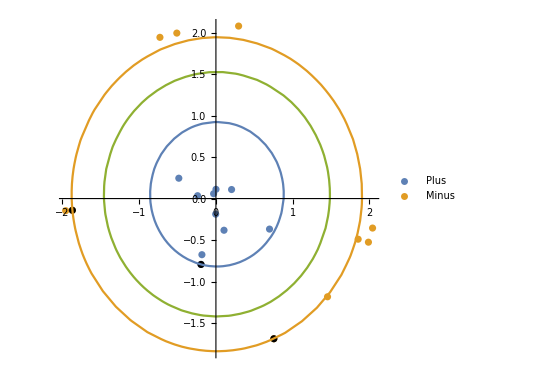

```mathematica
Show[ListPlot[Values[nonsepdata],AspectRatio->Full,PlotLegends->Keys[nonsepdata]],ListPlot[supportVectors3D,AspectRatio->Full,PlotStyle->Black],ContourPlot[Evaluate[Thread[{w1,w2,w3}.ϕ3D[{x0,y0}]+b=={1,-1,0}/.Join[wsolλ3D,bsolλ3D]]],{x0,-5,5},{y0,-5,5}],AspectRatio->Full,PlotRange->All]
```

### Implicit map using the Kernel trick

Instead of defining the map explicitly, the fact that our optimisation only depends on the inner product of samples means we can use the kernel trick. Let’s define a kernel k((x_i,y_i),(x_j,y_j))=x_i x_j+y_i y_j+(x_i^2+y_i^2)(x_j^2+y_j^2)

```mathematica
k[{xi_,yi_},{xj_,yj_}]:=xi xj+yi yj+(xi^2+yi^2) (xj^2+yj^2);
```

We now set up the dual optimisation problem by computing X X^T directly using the kernel:

```mathematica
xi=Join@@nonsepdata
```

{{-0.19418,-0.79399},{0.000940266,0.111416},{0.698568,-0.367905},{-0.00295604,-0.18778},{-0.238882,0.0345008},{-0.0299047,0.0585431},{-0.48357,0.245339},{0.203907,0.108877},{0.105382,-0.381727},{-0.182496,-0.676283},{2.04125,-0.355395},{-0.729497,1.94307},{-1.95821,-0.14589},{0.754913,-1.68958},{-0.509438,1.99432},{-1.87061,-0.141048},{1.45436,-1.18364},{1.85357,-0.489567},{1.98746,-0.525699},{0.295681,2.07913}}

```mathematica
Y=Join[ConstantArray[1,Length[nonsepdata["Plus"]]],ConstantArray[-1,Length[nonsepdata["Minus"]]]];
```

```mathematica
e=ConstantArray[1,Length[xi]];
```

```mathematica
λ=Table[λi[i],{i,Length[xi]}];
```

```mathematica
functionToMaximise=-1/2 Sum[λi[i]λi[j]Y[[i]]Y[[j]]k[xi[[i]],xi[[j]]],{i,Length[xi]},{j,Length[xi]}]+λ.e;
```

```mathematica
{maxk,solλk}=NMaximize[{functionToMaximise,λ>0,λ.Y==0},λ];
```

```mathematica
solλk//Chop
```

{λi[1]→0.253444,λi[2]→0,λi[3]→0,λi[4]→0,λi[5]→0,λi[6]→0,λi[7]→0,λi[8]→0,λi[9]→0,λi[10]→0,λi[11]→0,λi[12]→0,λi[13]→0,λi[14]→0.154863,λi[15]→0,λi[16]→0.09858,λi[17]→0,λi[18]→0,λi[19]→0,λi[20]→0}

We have now found the solution. In fact, it’s the exact same solution as we found with the 3D map because this kernel is exactly the one you get from that map.

### Generic Kernels

In the example so far we had a good idea for which kernel to use a priori. That is not usually the case so let’s now look at using some generic kernels. We will apply it to the following dataset:

```mathematica
data=<|Blue->{{1,1.2},{1.3,0.9},{0.9,1.2},{2.1,2.2},{2.3,2.9},{2.9,2.2}},Orange->{{2.1,1.2},{2.3,0.9},{2.7,1.2},{1.1,2.2},{1.3,2.9},{0.9,2.2}}|>;
```

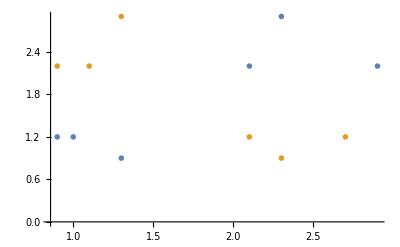

```mathematica
ListPlot[Values[data],PlotMarkers->"OpenMarkers"]
```

We could implement the kernels ourselves, take care of projecting back to the original space, etc., but let’s now just use the high-level Classify function to take care of all of those details for us. We will specify the “SupportVectorMachine” method with three different choices of kernel. Note that this generates a function that can return a probability that the input is of a given class.

First, with a linear kernel it fails totally

```mathematica
fL=Classify[data,Method->{"SupportVectorMachine","KernelType"->"Linear"}]
```

ClassifierFunction[…]

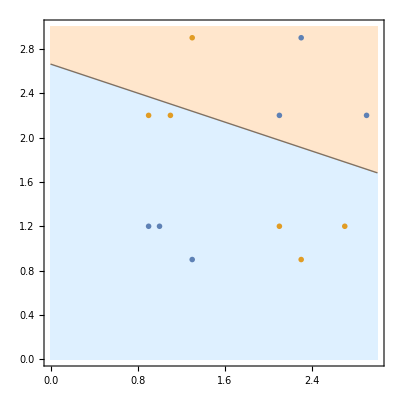

```mathematica
Show[ContourPlot[fL[{x,y},"Probability"->Orange],{x,0,3},{y,0,3},Evaluated->False,ContourShading->{LightBlue,LightOrange},Contours->{1/2}],ListPlot[Values[data],PlotMarkers->"OpenMarkers"]]
```

Next, the polynomial kernel does quite a good job in this case

```mathematica
fP=Classify[data,Method->{"SupportVectorMachine","KernelType"->"Polynomial","GammaScalingParameter"->2}]
```

ClassifierFunction[…]

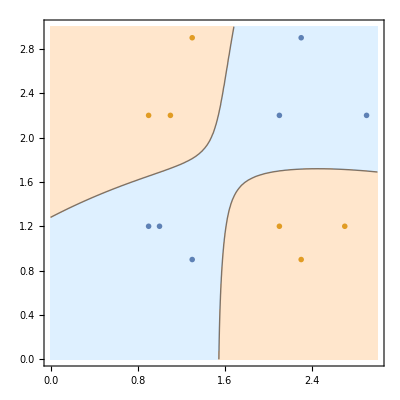

```mathematica
Show[ContourPlot[fP[{x,y},"Probability"->Orange],{x,0,3},{y,0,3},Evaluated->False,ContourShading->{LightBlue,LightOrange},Contours->{1/2}],ListPlot[Values[data],PlotMarkers->"OpenMarkers"]]
```

The Gaussian/radial basis function kernel does a good job

```mathematica
fR=Classify[data,Method->{"SupportVectorMachine","KernelType"->"RadialBasisFunction","GammaScalingParameter"->1/(2 0.4^2)}]
```

ClassifierFunction[…]

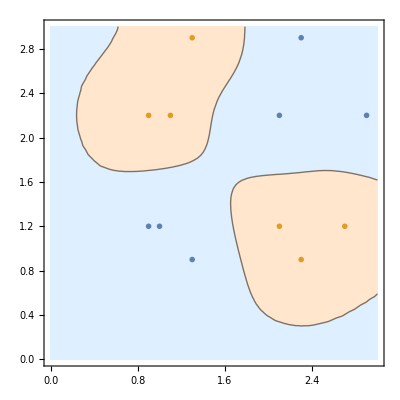

```mathematica
Show[ContourPlot[fR[{x,y},"Probability"->Orange],{x,0,3},{y,0,3},Evaluated->False,ContourShading->{LightBlue,LightOrange},Contours->{1/2}],ListPlot[Values[data],PlotMarkers->"OpenMarkers"]]
```

## Handwriting recognition: Suppor Vector Machine with MNIST Digits dataset

We now return to the example of handwriting recognition to see how well support vector machines perform with categorising the MNIST Digits dataset

```mathematica
MNIST=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
```

```mathematica
MNISTtest=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
MNISTbynumber=GroupBy[MNIST,Last->First];
```

We will train our support vector machine with a random sample of 100 digits.

```mathematica
trainingset=RandomSample[MNIST,100];
```

```mathematica
cf=Classify[trainingset, Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
Information[cf]
```

Classifier information
Data type | Image
Number of classes | 10
Accuracy | (67.15.) %
Method | SupportVectorMachine
Single evaluation time | 30.3 ms/example
Batch evaluation speed | 714. examples/s
Loss | 1.32 ± 0.18
Model memory | 2.16 MB
Training examples used | 100 examples
Training time | 6.67 s
 |

```mathematica
cf[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,1,3,3,9,1,0,7,8,9}

Let’s see how well it performs by testing it on a random sample of the test data

```mathematica
Tally[Map[cf[#[[1]]]==#[[2]]&,RandomSample[MNISTtest,1000]]]
```

{{False,851},{True,149}}

It’s right about 15% of the time - only slightly better than random luck. We could improve this by going back to the training step and using more training samples:

```mathematica
trainingset=RandomSample[MNIST,1000];
```

```mathematica
bettercf=Classify[trainingset, Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
Information[bettercf]
```

Classifier information
Data type | Image
Number of classes | 10
Accuracy | (89.53.2) %
Method | SupportVectorMachine
Single evaluation time | 42.6 ms/example
Batch evaluation speed | 480. examples/s
Loss | 0.411 ± 0.1
Model memory | 24. MB
Training examples used | 1000 examples
Training time | 29.7 s
 |

Let’s see how well it performs by testing it on a random sample of the test data

```mathematica
Tally[Map[bettercf[#[[1]]]==#[[2]]&,RandomSample[MNISTtest,1000]]]
```

{{True,876},{False,124}}

Now this is close to 90% accurate

```mathematica
Sort[Tally[Map[bettercf,RandomSample[MNISTbynumber[8],1000]]]]
```

{{0,4},{1,26},{2,16},{3,34},{4,9},{5,65},{6,13},{7,9},{8,800},{9,24}}